## Definiciones

```mathematica
ClearAll[Shift,Coin,DTQWStep];
Shift[t_]:=SparseArray[Join[Table[{i,i+2},{i,Range[2,#-2,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1.,{#,#}]&[2*(2*t+1)]

Coin[t_]:=KroneckerProduct[IdentityMatrix[2 t+1,SparseArray],SparseArray[FourierMatrix[2]]]
Coin[t_,c_]:=KroneckerProduct[IdentityMatrix[2 t+1,SparseArray],c]

DTQWStep[t_]:=Shift[t].Coin[t]
DTQWStep[t_,c_]:=Shift[t].Coin[t,c]
```

```mathematica
DTQW[ψ0_,t_]:=Module[{ψtMinus1},ψtMinus1=ArrayPad[ψ0,2];Do[ψtMinus1=ArrayPad[Chop[#.ψtMinus1]&[DTQWStep[i]],2],{i,t}];ψtMinus1]
DTQW[ψ0_,t_,c_]:=
Module[{ψtMinus1},
ψtMinus1=ArrayPad[ψ0,2];
Do[ψtMinus1=ArrayPad[Chop[#.ψtMinus1]&[DTQWStep[i,c]],2],{i,t}];
ψtMinus1
]
```

```mathematica
PositionProbabilityDistribution[ψ_,tmax_]:=Chop[Total[Abs[ψ[[#;;#+1]]]^2]&/@Range[1,2*(2*tmax+3),2]]
```

## Cálculos

```mathematica
t=1000;ψ0={1,1}/√2.;
ψ=DTQW[ψ0,t];
prob=PositionProbabilityDistribution[ψ,t];
```

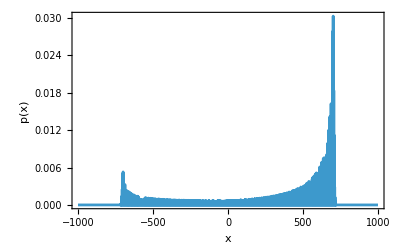

```mathematica
ListPlot[Transpose[{Range[-(t+1),t+1],prob}],
Joined->True,
PlotRange->Full,
Frame->True,
FrameStyle->Directive[Black,FontSize->18],
FrameLabel->{TraditionalForm[HoldForm[x]],TraditionalForm[p[x]]},
ImageSize->400
]
```

Varianza de la posición como función del tiempo:

```mathematica
t=1000;ψ0={1,1}/√2.;
variance=Table[
ψ=DTQW[ψ0,t];
prob=PositionProbabilityDistribution[ψ,t];
{t,Total[prob*Range[-(t+1),t+1]^2]-Total[prob*Range[-(t+1),t+1]]^2}
,{t,0,50}];
```

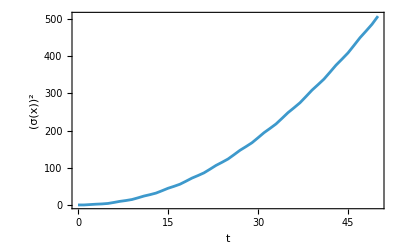

```mathematica
ListPlot[variance,
Joined->True,
PlotRange->Full,
Frame->True,
FrameStyle->Directive[Black,FontSize->18],
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[σ[x]^2]},
ImageSize->400
]
```

```mathematica
fitVariance=Fit[variance,{x^2},x]
```

0.202213 x^2

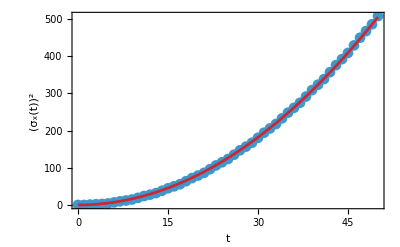

```mathematica
Show[
ListPlot[variance,
Joined->True,
PlotMarkers->Automatic,
PlotRange->Full,
Frame->True,
FrameStyle->Directive[Black,FontSize->18],
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[Subscript[σ, x][HoldForm[t]]^2]},
ImageSize->400
],
Plot[fitVariance,{x,Min[variance[[All,1]]],Max[variance[[All,1]]]},
PlotStyle->Directive[Red,Opacity[0.75]]
]
]
```

### C=σ_x

```mathematica
t=1000;ψ0={1,1}/√2.;
varianceSigmaX=Table[
ψ=DTQW[ψ0,t];
prob=PositionProbabilityDistribution[ψ,t];
{t,Total[prob*Range[-(t+1),t+1]^2]-Total[prob*Range[-(t+1),t+1]]^2}
,{t,0,50}];
```

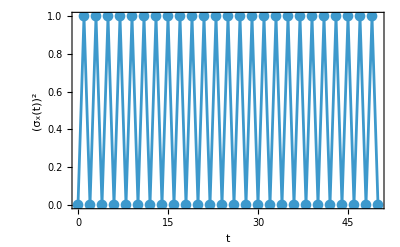

```mathematica
ListPlot[{varianceSigmaX},
Joined->True,
PlotMarkers->Automatic,
PlotRange->Full,
Frame->True,
FrameStyle->Directive[Black,FontSize->18],
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[Subscript[σ, x][HoldForm[t]]^2]},
ImageSize->400
]
```

### Estado aleatorio

```mathematica
(*Generar un punto aleatorio en la superficie de una esfera unitaria*)
randomPoint=RandomPoint[Sphere[]];
(*Convertir coordenadas cartesianas a esféricas (theta y phi)*)
{theta,phi}=CoordinateTransformData["Cartesian"->"Spherical","Mapping",randomPoint][[2;;3]];
ψ0={Cos[theta/2],Exp[I*phi]Sin[theta/2]};

t=100;
ψ=DTQW[ψ0,t];
prob=PositionProbabilityDistribution[ψ,t];
```

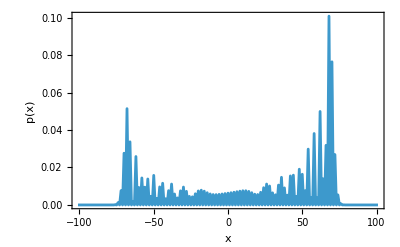

```mathematica
ListPlot[Transpose[{Range[-(t+1),t+1],prob}],
Joined->True,
PlotRange->Full,
Frame->True,
FrameStyle->Directive[Black,FontSize->18],
FrameLabel->{TraditionalForm[HoldForm[x]],TraditionalForm[p[x]]},
ImageSize->400
]
```

### Rotación alrededor de y como la moneda

```mathematica
t=250;ψ0={1.,I}/√2.;c=MatrixExp[-I*2Pi*RandomReal[]*PauliMatrix[2]];
ψ=DTQW[ψ0,t];
prob=PositionProbabilityDistribution[ψ,t];
```

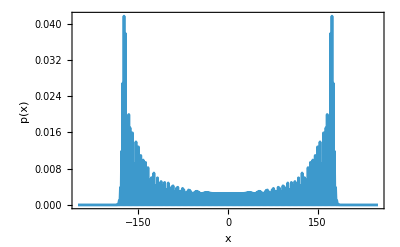

```mathematica
ListPlot[Transpose[{Range[-(t+1),t+1],prob}],
Joined->True,
PlotRange->Full,
Frame->True,
FrameStyle->Directive[Black,FontSize->18],
FrameLabel->{TraditionalForm[HoldForm[x]],TraditionalForm[p[x]]},
ImageSize->400
]
```

```mathematica
t=250;ψ0={1.,0};c=MatrixExp[-I*2Pi*RandomReal[]*PauliMatrix[2]];
ψ=DTQW[ψ0,t];
prob=PositionProbabilityDistribution[ψ,t];
```

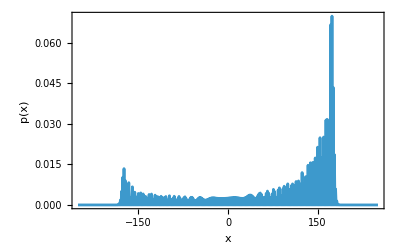

```mathematica
ListPlot[Transpose[{Range[-(t+1),t+1],prob}],
Joined->True,
PlotRange->Full,
Frame->True,
FrameStyle->Directive[Black,FontSize->18],
FrameLabel->{TraditionalForm[HoldForm[x]],TraditionalForm[p[x]]},
ImageSize->400
]
```

```mathematica
t=250;ψ0=Normalize[{1.-√2.,1.}];c=FourierMatrix[2];
ψ=DTQW[ψ0,t];
prob=PositionProbabilityDistribution[ψ,t];
```

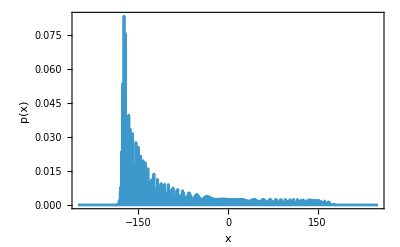

```mathematica
ListPlot[Transpose[{Range[-(t+1),t+1],prob}],
Joined->True,
PlotRange->Full,
Frame->True,
FrameStyle->Directive[Black,FontSize->18],
FrameLabel->{TraditionalForm[HoldForm[x]],TraditionalForm[p[x]]},
ImageSize->400
]
```

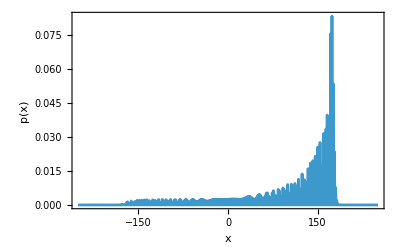

```mathematica
t=250;ψ0=Normalize[{1.+√2.,1.}];c=FourierMatrix[2];
ψ=DTQW[ψ0,t];
prob=PositionProbabilityDistribution[ψ,t];
ListPlot[Transpose[{Range[-(t+1),t+1],prob}],
Joined->True,
PlotRange->Full,
Frame->True,
FrameStyle->Directive[Black,FontSize->18],
FrameLabel->{TraditionalForm[HoldForm[x]],TraditionalForm[p[x]]},
ImageSize->400
]
```

```mathematica
t=250;ψ0={Cos[Pi/8.],Sin[Pi/8.]};c=SparseArray[FourierMatrix[2]];
ψ=DTQW[ψ0,t];
prob=PositionProbabilityDistribution[ψ,t];
ListPlot[Transpose[{Range[-(t+1),t+1],prob}],
Joined->True,
PlotRange->Full,
Frame->True,
FrameStyle->Directive[Black,FontSize->18],
FrameLabel->{TraditionalForm[HoldForm[x]],TraditionalForm[p[x]]},
ImageSize->400
]
```

-Graphics-

```mathematica
{ψ0,FourierMatrix[2].ψ0}
```

{{0.92388,-0.382683},{0.382683,0.92388}}

## Cálculos Mariana

```mathematica
t=250;ψ0={1.,0.};
ψ=DTQW[ψ0,t];
prob=PositionProbabilityDistribution[ψ,t];
```

```mathematica
ListPlot[Transpose[{Range[-(t+1),t+1],prob}],
Joined->True,
PlotRange->Full,
Frame->True,
FrameStyle->Directive[Black,FontSize->18],
FrameLabel->{TraditionalForm[HoldForm[x]],TraditionalForm[p[x]]},
ImageSize->400
]
```

-Graphics-

### Moneda dependiente de la posición de Mittal and Huang 2024, ecuación (9)

```mathematica
MatrixExp[-I*θ*PauliMatrix[2]/2]
```

{{Cos[θ/2],-Sin[θ/2]},{Sin[θ/2],Cos[θ/2]}}

```mathematica
ThetaB[θBPlus_,θBMinus_,x_]:=(θBPlus(1.+Tanh[N[x]])+θBMinus(1.-Tanh[N[x]]))/2.
```

```mathematica
t=100;
thetas=ThetaB[Pi/4.,-Pi/8.,#]&/@Range[-t,t];
blocks={{Cos[#/2],-Sin[#/2]},{Sin[#/2],Cos[#/2]}}&/@thetas;
BlockDiagonalMatrix[blocks,TargetStructure->"Sparse"]
```

SparseArray[…]

```mathematica
Coin[t_,θBMinus_,θBPlus_]:=
Module[{thetas,blocks},
thetas=ThetaB[θBPlus,θBMinus,#]&/@Range[-t,t];
blocks={{Cos[#/2.],-Sin[#/2.]},{Sin[#/2.],Cos[#/2.]}}&/@thetas;
BlockDiagonalMatrix[blocks,TargetStructure->"Sparse"]
]
```

```mathematica
Coin[2,Pi/4.,-Pi/8.]
```

SparseArray[…]

```mathematica
DTQWStep[t_,θBPlus_,θBMinus_]:=Shift[t].Coin[t,θBMinus,θBPlus]
```

```mathematica
DTQW[ψ0_,t_,θBPlus_,θBMinus_]:=Module[{ψtMinus1},ψtMinus1=ArrayPad[ψ0,2];Do[ψtMinus1=ArrayPad[Chop[#.ψtMinus1]&[DTQWStep[i,θBPlus,θBMinus]],2],{i,t}];ψtMinus1]
```

```mathematica
t=500;ψ0={0.,1.};{θBMinus,θBPlus}={-Pi/8.,Pi/4.};
RepeatedTiming[ψ=DTQW[ψ0,t,θBPlus,θBPlus];]
```

{2.78791,Null}

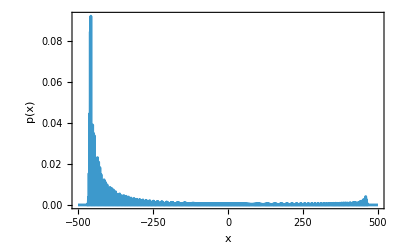

```mathematica
prob=PositionProbabilityDistribution[ψ,t];
ListPlot[Transpose[{Range[-(t+1),t+1],prob}],
Joined->True,
PlotRange->Full,
Frame->True,
FrameStyle->Directive[Black,FontSize->18],
FrameLabel->{TraditionalForm[HoldForm[x]],TraditionalForm[p[x]]},
ImageSize->400
]
```

## Idea de Carlos vs mi algoritmo

```mathematica
ψ=ArrayPad[{1,I}/√2.,2];
AbsoluteTiming[Do[ψ=ArrayPad[Chop[#.ψ]&[DTQWStep[t]],2],{t,1000}]]
```

{2.98371,Null}

```mathematica
AbsoluteTiming[Eigensystem[DTQWStep[1000]];]
```

Eigensystem::arh: Because finding 4002 out of the 4002 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

{32.7933,Null}